## Zestaw 7

Katarzyna Sowa

## 3N

Szukanie minium funkcji Rosenbrocka metoda Levengerga-Marquardta. 
Wykorzystujemy wbudowana funkcje Mathematici "FindMinimum" z opcja "LevenbergMarquardt".

```mathematica
f[{x_,y_}]=100 (y-x^2)^2+(1-x)^2;
```

```mathematica
FindMinimum[100 (y-x^2)^2+(1-x)^2,{x,0.1},{y,0.1},Method->"LevenbergMarquardt"]
```

{0.,{x→1.,y→1.}}

```mathematica
FindMinimum[100 (y-x^2)^2+(1-x)^2,{x,0.5},{y,0.1},Method->"LevenbergMarquardt"]
```

{0.,{x→1.,y→1.}}

```mathematica
FindMinimum[100 (y-x^2)^2+(1-x)^2,{x,1.5},{y,2.1},Method->"LevenbergMarquardt"]
```

{0.,{x→1.,y→1.}}

```mathematica
FindMinimum[100 (y-x^2)^2+(1-x)^2,{x,Random[]},{y,Random[]},Method->"LevenbergMarquardt"]
```

{1.2326×10^-32,{x→1.,y→1.}}

```mathematica
i=0;
```

```mathematica
pts = Reap[FindMinimum[100 (y-x^2)^2+(1-x)^2,{x,0.1},{y,0.1},Method->"LevenbergMarquardt",StepMonitor:>{Sow[{x,y}],i++}]][[2,1]];Print["Potrzeba ", i ," krokow"];
pts =Join[{{-1.2,1}},pts];
```

Potrzeba 9 krokow

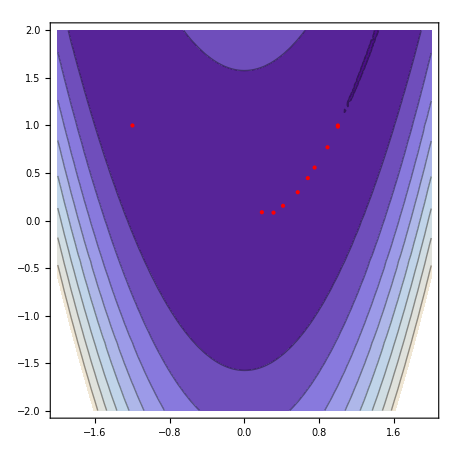

```mathematica
ContourPlot[100 (y-x^2)^2+(1-x),{x,-2,2},{y,-2,2},Epilog->{Red,Point[pts]}]
```